```mathematica
WaveR[Z_,r_,n_,l_]:=Module[{unit,tmp},unit=(1/(2l+1)!)Sqrt[(n+1)!/(2n (n-l-1)!)](((2Z)/n)^(l+3/2));
tmp=unit r^l Exp[-((Z r)/n)]Hypergeometric1F1[l+1-n,2l+2,(2Z r)/n]];
```

Z=1时，不同主量子数和角量子数下径向波函数模平方的比较

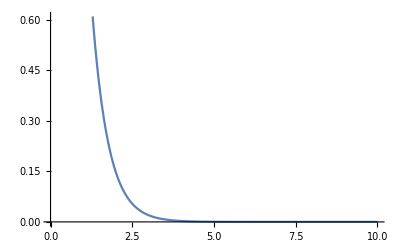

```mathematica
Z=1;n=1;
Plot[Table[WaveR[Z,r,n,i]^2,{i,0,n-1}]//Evaluate,{r,0,10},PlotLegends->"l=0"]
```

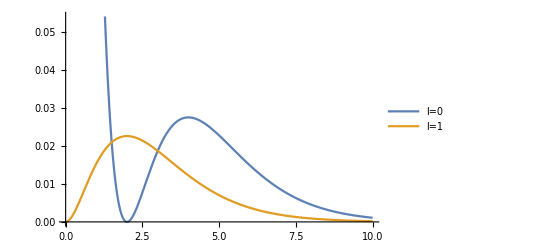

```mathematica
Z=1;n=2;
Plot[Table[WaveR[Z,r,n,i]^2,{i,0,n-1}]//Evaluate,{r,0,10},PlotLegends->{"l=0","l=1"}]
```

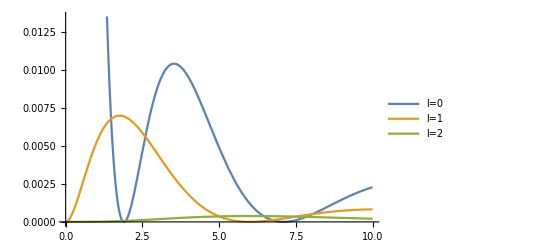

```mathematica
Z=1;n=3;
Plot[Table[WaveR[Z,r,n,i]^2,{i,0,n-1}]//Evaluate,{r,0,10},PlotLegends->{"l=0","l=1","l=2"}]
```

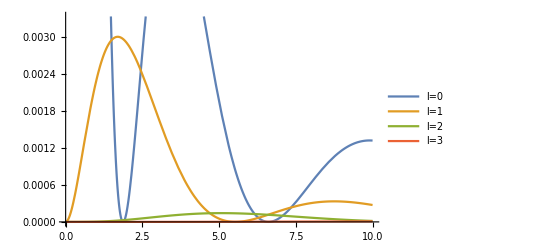

```mathematica
Z=1;n=4;
Plot[Table[WaveR[Z,r,n,i]^2,{i,0,n-1}]//Evaluate,{r,0,10},PlotLegends->{"l=0","l=1","l=2","l=3"}]
```

Z不同，n=1,l=0时径向波函数模平方的比较

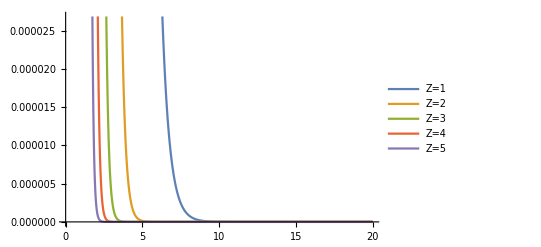

```mathematica
(*远处*)
n=1;l=0;
Plot[Table[WaveR[Z,r,n,l]^2,{Z,1,5}]//Evaluate,{r,0,20},PlotLegends->{"Z=1","Z=2","Z=3","Z=4","Z=5"}]
```

```mathematica
(*近处*)
```

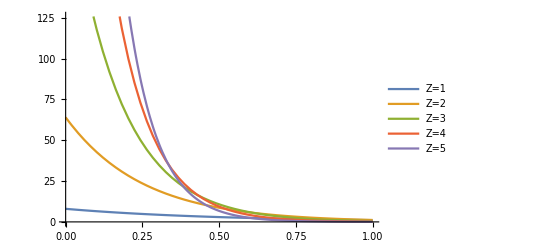

```mathematica
Plot[Table[WaveR[Z,r,n,l]^2,{Z,1,5}]//Evaluate,{r,0,1},PlotLegends->{"Z=1","Z=2","Z=3","Z=4","Z=5"}]
```